```mathematica
vDiseasePrior = {0.75,0.25};
```

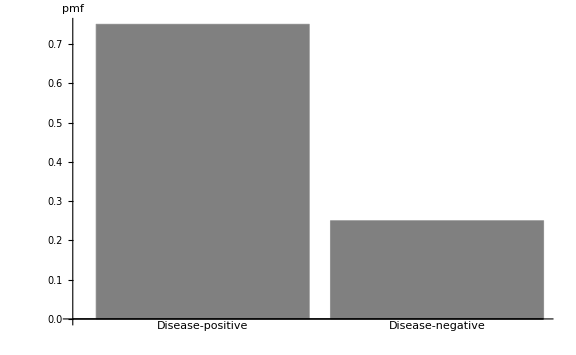

```mathematica
p1=BarChart[vDiseasePrior,ChartStyle->{Gray},BaseStyle->{FontSize->16},AxesLabel->{pmf},ChartLabels->{"Disease-positive","Disease-negative"}]
```

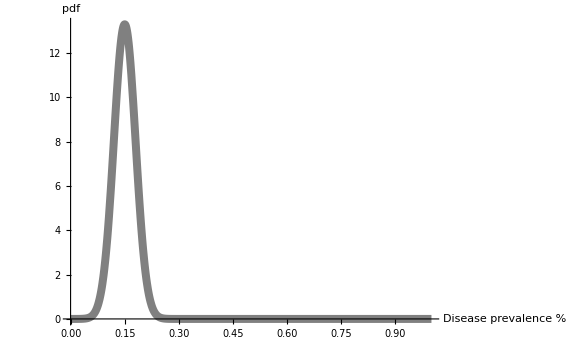

```mathematica
p2=Show[Plot[PDF[NormalDistribution[0.15,0.03],x],{x,0,1},PlotRange->{{0,1},Full},PlotStyle->{Gray,Thickness[0.01]},BaseStyle->{FontSize->16},AxesLabel->{"Disease prevalence %","pdf"}],ImageSize->Large]
```

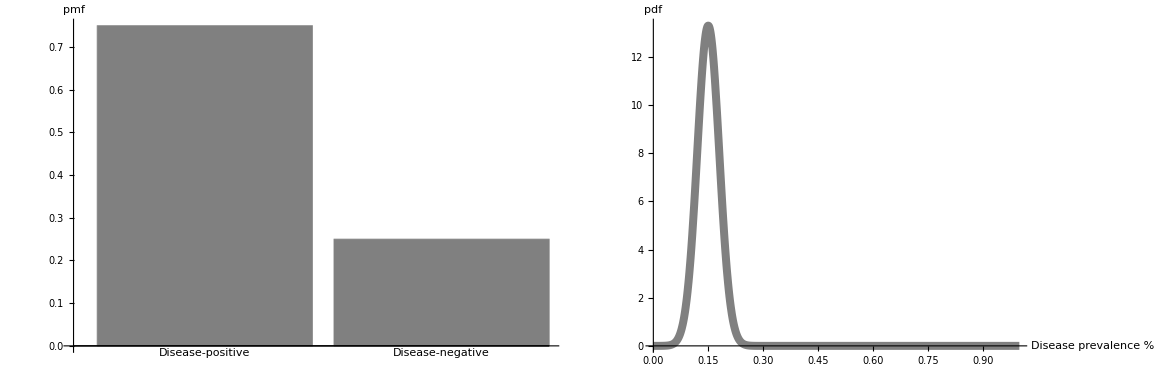

```mathematica
GraphicsRow[{p1,p2},Spacings->{0,Automatic}]
```